## 3.029 Spring 2022 Lectures 09 & 10 - 02/28/2022, 03/02/2022

## Polymer Microstructures and Statistics

We’ll take a small detour from our thermodynamics lectures, and present some material related to your synthesis class, 3.023

The idea here is to start from simple models, and add complexity as needed to explain various concepts you saw/will see in lecture

## Polymers as Random Walks

We will treat polymers effectively as 1-D chains of fixed-length molecular units (embedded in either 2D or 3D)

Using these assumptions, the simplest model of a polymer microstructure is a sequence of uncorrelated (or random) bond angles

This can be modeled with a random walk!

### (Aside) Random Walks

#### Lattice Walk

Imagine we have some random walkers (molecules, vacancies, drunken sailors..)

Which take steps on a square lattice using equal probabilities

First, let’s get a list of the possible steps (including staying still)

```mathematica
steps=Select[Tuples[Range[-1,1],2],Norm[#]<=1&]
```

{{-1,0},{0,-1},{0,0},{0,1},{1,0}}

At each step, we have an equal probability of choosing one of these steps

```mathematica
squareLatticeStep[]:=RandomChoice[steps]
```

For example 10 such steps:

```mathematica
Table[squareLatticeStep[],10]
```

{{0,-1},{1,0},{0,-1},{-1,0},{0,-1},{0,0},{0,-1},{0,0},{0,-1},{0,1}}

Starting from the origin, we can accumulate these steps to see where our random walker ends up

```mathematica
Accumulate[Prepend[Table[squareLatticeStep[],10],{0,0}]]
```

{{0,0},{0,1},{0,1},{-1,1},{0,1},{0,0},{0,-1},{0,-1},{1,-1},{1,0},{1,-1}}

Let’s visualize our random-walker’s path by drawing a line through our trajectory

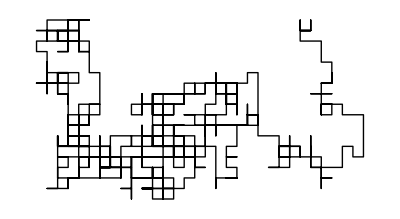

```mathematica
Prepend[Table[squareLatticeStep[],1000],{0,0}]//Accumulate//Line//Graphics
```

We can make a better-looking visualization by using disks and opacity for our visited locations

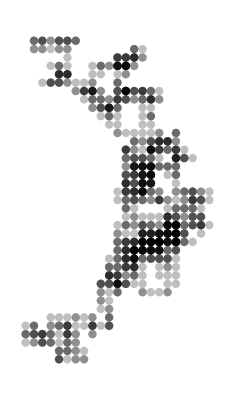

```mathematica
With[{locations=Accumulate[Prepend[Table[squareLatticeStep[],1000],{0,0}]]},
Graphics[{Opacity[0.25],Disk[#,1/2]&/@locations}]]
```

#### Variable Angle Walk

Let’s relax our lattice-constraint, by allowing our walkers to take unit steps at any angle

```mathematica
randomUnitStep[]:=Module[{θ=RandomReal[{0,2 Pi}]},{Cos[θ],Sin[θ]}]
```

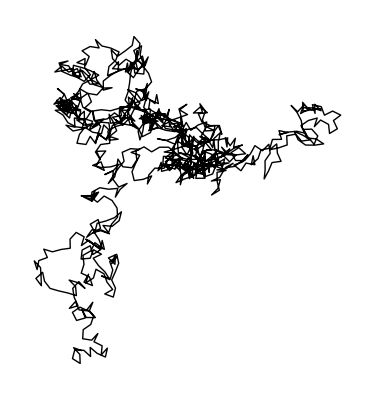

```mathematica
Prepend[Table[randomUnitStep[],1000],{0,0}]//Accumulate//Line//Graphics
```

Let’s visualize this slightly better, tracking the walkers’ progress in a periodic box

```mathematica
With[{steps=Mod[Accumulate[Prepend[Table[randomUnitStep[],10000],{0,0}]],50,-25]},

Animate[
Graphics[{Opacity[0.25],Disk[#,1/2]&/@Take[steps,time]},
PlotRange->25{{-1,1},{-1,1}}],{time,1,10000,1},
AnimationRunning->False,AnimationRepetitions->1,AnimationRate->100,Paneled->False]]
```

#### Angle Path

At this point, it’s convenient to use the built-in AnglePath to construct these

```mathematica
?AnglePath
```

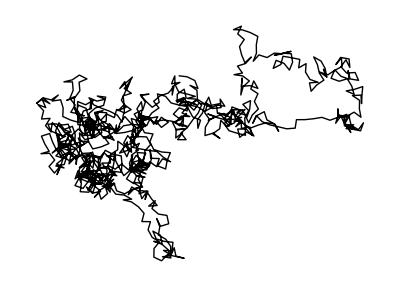

```mathematica
RandomReal[{0,2π},1000]//AnglePath//Line//Graphics
```

Let’s see if we can vary the length of the step

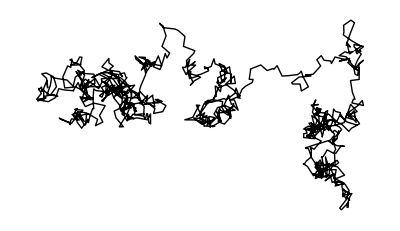

```mathematica
With[{
randomAngles=RandomReal[{0,2π},1000],
randomLengths=RandomReal[{0,1},1000]
},
AnglePath[Transpose[{randomLengths,randomAngles}]]//Line//Graphics
]
```

#### A fun application: L-Systems

L-systems or “Lindenmayer Systems” originated from botany and refers to recursive systems used to model variety of organisms using:

An alphabet

An axiom (or initial state)

Rules

Algae growth

Alphabet: “A” & “B”

Axiom: “A”

Rules: (“A” → “AB”) & (“B”→ “A”)

-Graphics-

We can quickly implement this algae-growth as a one-liner:

```mathematica
?StringReplace
```

```mathematica
StringReplace["ABCD",{"A"->"AB","B"->"A"}]
```

ABACD

```mathematica
NestList[StringReplace[#,{"A"->"AB","B"->"A"}]&,"A",4]
```

{A,AB,ABA,ABAAB,ABAABABA}

```mathematica
Column[NestList[StringReplace[#,{"A"->"AB","B"->"A"}]&,"A",4],Center]
```

A
AB
ABA
ABAAB
ABAABABA

Most operations of interest can be defined using the following “standard” alphabet

F:	Draw line & move forward

G:	Move forward (without drawing a line)

+:	Turn right (by a specified angle)

-:	Turn left (by a specified angle)

This is commonly referred to as “Turtle graphics”.
Imagine a turtle sitting on your computer screen following a limited set of commands.

We can ab(use) AnglePath to quickly specify our turtle’s path!

E.g. for this mysterious rule-set

```mathematica
Short[seq=Last[SubstitutionSystem[{"X"->"X+YF+","Y"->"-FX-Y"},"FX",12]]]
```

FX+YF++-FX-YF++-FX+YF+--FX-YF++-FX+YF++-FX-YF…FX+YF+--FX-YF+--FX+YF++-FX-YF+--FX+YF+--FX-YF+

```mathematica
StringCases[seq,
{"F"->{1,0},"X"->{0,0},"Y"->{0,0},"+"->{0,Pi/2},"-"->{0,-Pi/2}}]//Short
```

{{1,0},{0,0},{0,π/2},{0,0},{1,0},{0,π/2},{0,π/2},«16369»,{1,0},{0,0},{0,-π/2},{0,0},{1,0},{0,π/2}}

```mathematica
StringCases[seq,
{"F"->{1,0},"X"->{0,0},"Y"->{0,0},"+"->{0,Pi/2},"-"->{0,-Pi/2}}
]//AnglePath//Line//Graphics
```

Or this one

```mathematica
With[{seq=Last[SubstitutionSystem[{"F"->"G+F+G","G"->"F-G-F"},"F",{8}]]},
StringCases[seq,
{"F"->{1,0},"G"->{1,0},"+"->{0,Pi/3},"-"->{0,-Pi/3}}
]//AnglePath//Line//Graphics
]
```

Or this diffusion-limited-aggregation inspired one

```mathematica
With[{seq=Last[SubstitutionSystem[{"F"->"FF+F++F+F"},"F+F+F+F",{6}]]},
StringCases[seq,
{"F"->{1,0},"+"->{0,Pi/2}}
]//AnglePath//Line//Graphics
]
```

If you found these fun, there’s more examples here!

### Back to Polymers

We can visualize a polymer with 32 monomers of fixed length and random bond-angled in 2D

Note: we will fix the bond-length to be equal to 2 (so that we can visualize monomers as disks/spheres of radius 1)

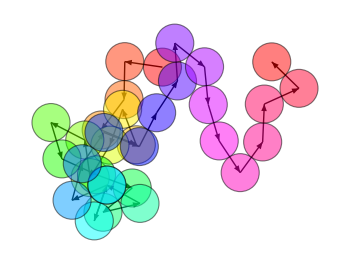

```mathematica
Block[{steps=AngleVector[{2,#}]&/@RandomReal[{0,2π},32],positions},
positions = Prepend[Accumulate[steps],{0,0}];
Graphics[]
]
```

This is easy to extend to 3D

We just need take random steps on the surface of a sphere with radius 2

```mathematica
Block[{steps=RandomPoint[Sphere[{0,0,0},2],32],positions},
positions = Prepend[Accumulate[steps],{0,0,0}];
Graphics3D[]
]
```

-Graphics3D-

Let’s investigate the expected length of such an “uncorrelated” polymer, as a function of the number of molecular units.

We’ll use a Monte-Carlo method to estimate this

I.e., we’ll generate a set of random walkers for a fixed number of units, and then compute the mean displacement from the origin.
We will then repeat this multiple times for each number of molecular units.

We write a simple function to do the following:

compute N random steps (in 1D, 2D, or 3D)

sum up all of the steps (to get to the last point in the walk)

compute how far that point is from the origin

```mathematica
displacement[nUnits_, dimension_/;1<= dimension<= 3]:=
 Norm[
Total[ (*net displacement vector*)
Switch[dimension,
1,RandomChoice[{-1,1},nUnits],
2,RandomPoint[Circle[],nUnits],
3,RandomPoint[Sphere[],nUnits]
]
]
]
```

Note:  Coding comment - The above is a natural way to write this function.
However, often times it’s cleaner to use “Multiple-dispatch” to specialize a function based on an argument

```mathematica
displacementMultipleDispatch[1][nUnits_]:= Norm[Total[ RandomChoice[{-1,1},nUnits]]]
displacementMultipleDispatch[2][nUnits_]:= Norm[Total[ RandomPoint[Circle[],nUnits]]]
displacementMultipleDispatch[3][nUnits_]:= Norm[Total[ RandomPoint[Sphere[],nUnits]]]
```

Let’s generate some data for 1D, 2D, and 3D

Takes ~30s

```mathematica
(*
displacementData [1]= Table[{2^units,displacementMultipleDispatch[1][2^units]},{units,10,18},1000];
displacementData [2]= Table[{2^units,displacementMultipleDispatch[2][2^units]},{units,10,18},1000];
*)
displacementData [3]= Table[{2^units,displacementMultipleDispatch[3][2^units]},{units,10,18},1000];
```

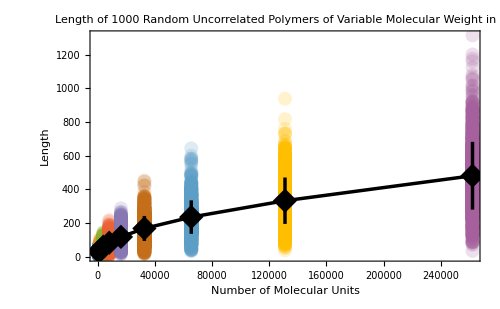

```mathematica
With[{
meanDisplacements = Mean/@displacementData[3],
standardDeviationDisplacements = StandardDeviation/@displacementData[3]
},
Show[
ListPlot[displacementData[3],],ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements,Last/@meanDisplacements,Last/@standardDeviationDisplacements}],]
]
]
```

Let’s see if we can discover the relationship between the expected length and the number of units

```mathematica
fitModel[3]=Block[{powerLawModel=a n^power,meanDisplacements=Mean/@displacementData[3],fit},
fit=Echo[FindFit[meanDisplacements,powerLawModel,{a,power},n]];
powerLawModel/.fit
]
```

{a→0.850777,power→0.5075}

0.850777 n^0.5075

The fit shows that the length increases as

In our simulation, each If each bond had length = 1

If the bond length were a, then the results would have been

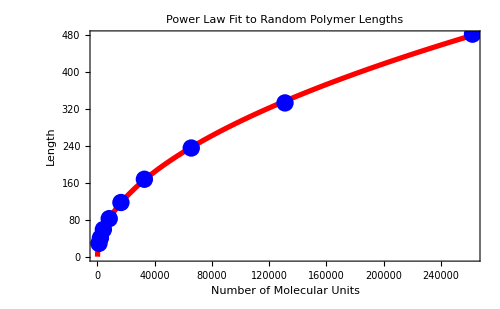

```mathematica
With[{meanDisplacements=Mean/@displacementData[3]},
Plot[fitModel[3],{n,1,2^18},Epilog->{Directive[Blue,PointSize[0.025]],Point[meanDisplacements]},]
]
```

Thus, we demonstrated that the expected length polymer with uncorrelated bond direction increases as the square-root of the number of molecular units.

## Models of “Stiff” Polymers

Above we called the random-walk polymer as “uncorrelated”

This is because each molecular unit was allowed to take any bond angle with the next molecular unit

Some polymers may be less “floppy”: there will be a smaller range of “bending angle” at each molecular unit.

This would create direction correlations in the polymer chain.

We can model this by creating a correlation in the steps by selecting new directions within a given angle of the previous angle.

In two dimensions, this would be an arc of a circle centered on the previous direction.

In three dimensions, this would be points withing a given solid angle on a sphere.

### 2D Polymer Correlations

We want to choose the next direction from a uniform distribution of angles around the last direction  Δϕ < θ < Δϕ

In-fact, our friend AnglePath does exactly this

```mathematica
Manipulate[
With[{steps = AnglePath[{2,#}&/@RandomReal[{-range/2,range/2},12]]},
Graphics[

]
],
{range,0,2Pi}
,Paneled->False]
```

### 3D Polymer Correlations

For 3D, we need to uniformly sample points from a uniform spatial distribution over a spherical cap

We will show a couple of ways to do this

#### Random Point

We start using a generalization of how we sampled points on a sphere earlier, using RandomPoint

To do this, we require a region specification of a spherical cap

E.g. using an algebraic description and Implicit Region

We will assume the spherical cap’s radius = 1

```mathematica
With[{height=3/4},
ImplicitRegion[x^2+y^2+z^2==1^2&&z>= height,{x,y,z}]//Region]
```

-Graphics3D-

This works, but the height specification is rather clunky

Instead, we’ll specify this using a solid-angle

```mathematica
Manipulate[
,
{{ϕ,π},0.1,4Pi},Paneled->False
]
```

The red circle above is  intersection of the cone and the sphere

The circle is located at a height z=Cos[ϕ/4] and has a radius r = Sin[ϕ/4]

```mathematica
Clear[implicitSphericalCap]
implicitSphericalCap[solidAngle_]:=implicitSphericalCap[solidAngle]=DiscretizeRegion[ImplicitRegion[x^2+y^2+z^2==1^2&&z>= Cos[solidAngle/4],{x,y,z}]]
```

```mathematica
implicitSphericalCap[π]
```

-Graphics3D-

We can now use RandomPoint to sample N points on this surface

```mathematica
Manipulate[
With[{reg=implicitSphericalCap[ϕ]},
Graphics3D[Point[RandomPoint[reg,numberOfPoints]]]],{{ϕ,π},0.1,4π},{{numberOfPoints,1000},100,10000},Paneled->False]
```

#### Symbolic Probability Density

This is rather costly

```mathematica
RandomPoint[implicitSphericalCap[π],10000];//RepeatedTiming
```

{0.00132973,Null}

Instead, we can construct a symbolic formula for sampling uniformly over a spherical cap

We start by noticing that the probability density of a random point on the sphere lying on the red circle intersection above, is proportional to the circumference

As such, the probability of finding an angle less than a solid angle α is proportional to

```mathematica
With[{r=Sin[ϕ/4]},
Integrate[r,{ϕ,0,α}]]
```

8 Sin[α/8]^2

Which we can normalize by a maximum solid angle α to give:

```mathematica
probability[αMax_][α_]=Integrate[Sin[ϕ/4],{ϕ,0,α}]/(8 Sin[αMax/8]^2)
```

Csc[αMax/8]^2 Sin[α/8]^2

We care to sweep the probability from a uniform 0 < p < 1, and calculate the angle α

So we need to invert this relationship

```mathematica
Solve[p==probability[αMax][α],α]/.C[_]:>0
```

{{α→-8 ArcSin[√p Sin[αMax/8]]},{α→8 (π-ArcSin[√p Sin[αMax/8]])},{α→8 ArcSin[√p Sin[αMax/8]]},{α→8 (π+ArcSin[√p Sin[αMax/8]])}}

```mathematica
randomPointSphericalCap[αMax_,n_]:=Block[{p=RandomReal[{0,1},n],ϕ,r,θ=RandomReal[{0,2Pi},n]},
ϕ =8 ArcSin[Sqrt[p]Sin[αMax/8]];
r = Sin[ϕ/4];
Transpose[{r Cos[θ],r Sin[θ],Cos[ϕ/4]}]
]
```

```mathematica
Manipulate[
Graphics3D[Point[randomPointSphericalCap[ϕ,numberOfPoints]]],{{ϕ,π},0.1,4π},{{numberOfPoints,1000},100,10000},Paneled->False]
```

This is indeed ~10x faster

```mathematica
randomPointSphericalCap[π,10000];//RepeatedTiming
```

{0.000225495,Null}

#### AnglePath3D

It would of-course be convenient if we could use a function similar to AnglePath but in 3D

The function does exist, but it’s usage is slightly more complicated

```mathematica
?AnglePath3D
```

We will use the rotation matrices version of the function above

We therefore need the matrix which moves a point from {0,0,1} to the random point we computed above

```mathematica
MatrixForm[rotationMatrix[{r_,θ_,ϕ_}]=Simplify[Simplify[RotationMatrix[{{0,0,1},{r Cos[θ],r Sin[θ],Cos[ϕ/4]}}],{r>0,2π>θ>0,4π>ϕ>0}]/.{Abs[a_]^2:>a^2},{r>0,2π>θ>0,4π>ϕ>0}]]
```

((√2 Cos[θ]^2 Cos[ϕ/4])/(√(1+2 r^2+Cos[ϕ/2]))+Tan[θ]^2/Abs[Sec[θ]]^2 | (√2 Cos[θ] Cos[ϕ/4] Sin[θ])/(√(1+2 r^2+Cos[ϕ/2]))-Tan[θ]/Abs[Sec[θ]]^2 | (√2 r Cos[θ])/(√(1+2 r^2+Cos[ϕ/2]))
(√2 Cos[θ] Cos[ϕ/4] Sin[θ])/(√(1+2 r^2+Cos[ϕ/2]))-Tan[θ]/Abs[Sec[θ]]^2 | 1/Abs[Sec[θ]]^2+(√2 Cos[ϕ/4] Sin[θ]^2)/(√(1+2 r^2+Cos[ϕ/2])) | (√2 r Sin[θ])/(√(1+2 r^2+Cos[ϕ/2]))
-(√2 r Cos[θ])/(√(1+2 r^2+Cos[ϕ/2])) | -(√2 r Sin[θ])/(√(1+2 r^2+Cos[ϕ/2])) | (√2 Cos[ϕ/4])/(√(1+2 r^2+Cos[ϕ/2])))

Let’s modify our function to do this quickly

```mathematica
randomPointSphericalCapRotationMatrix[αMax_,n_]:=Block[{p=RandomReal[{0,1},n],ϕ,r,θ=RandomReal[{0,2Pi},n]},
ϕ =8 ArcSin[Sqrt[p]Sin[αMax/8]];
r = Sin[ϕ/4];
Transpose[rotationMatrix[{r,θ,ϕ}],{2,3,1}]
]
```

```mathematica
MatrixForm/@randomPointSphericalCapRotationMatrix[Pi/6,3]
```

{(0.999806 | -0.000163905 | -0.0196973
-0.000163905 | 0.999862 | -0.0166396
0.0196973 | 0.0166396 | 0.999668),(0.999461 | 0.00139637 | -0.0328057
0.00139637 | 0.996384 | 0.0849525
0.0328057 | -0.0849525 | 0.995845),(0.997204 | 0.00184204 | -0.0747013
0.00184204 | 0.998786 | 0.0492186
0.0747013 | -0.0492186 | 0.995991)}

And make sure it makes sense visually

```mathematica
Graphics3D[Sphere[#,1/2]&/@AnglePath3D[randomPointSphericalCapRotationMatrix[π,25]]]
```

-Graphics3D-

From the AnglePath3D documentation
“the next position p_i={x_i,y_i,z_i} is obtained by p_i=p_(i-1)+f_i.{r_i,0,0}, with the frame rotation matrix f_i given by f_i=f_(i-1).mat_i and f_0=mat_0.”

What AnglePath3D does is equivalent to a “Folding” a dot-product over the list of rotations:
  
and then accumulating the vectors in the list:

```mathematica
?AnglePath3D
```

The built-in method is somewhat slow again

```mathematica
rotations=randomPointSphericalCapRotationMatrix[π,10000];
{timingAP,lastPosAP} =RepeatedTiming[Last[pathAP =AnglePath3D[rotations]]]
```

{0.018257,{-187.63,-497.677,-53.2546}}

Let’s see if we can reproduce this using FoldList

```mathematica
?FoldList
```

```mathematica
{timingFP1,lastPosFP1} =RepeatedTiming[Last@Accumulate[pathFP1=(#.{1,0,0})&/@FoldList[Dot,rotations]]]
```

{0.00382815,{-187.63,-497.677,-53.2546}}

You’ll notice two things:

i) This is indeed much faster, even for  10000 rotations

ii) The end points are the same, meaning the two methods are equivalent

Moreover, the Dot product above    picks out the first column of

Instead of the Dot product, we can grab the column:

```mathematica
{timingFP2,lastPosFP2} =RepeatedTiming[Last@Accumulate[pathFP2=(#[[All,1]])&/@FoldList[Dot,rotations]]]
```

{0.00446229,{-187.63,-497.677,-53.2546}}

Note: this isn’t faster since we’re do this for each rotation, but we can also grab all the columns at once

```mathematica
{timingFP3,lastPosFP3} =RepeatedTiming[Last@Accumulate[pathFP3=(FoldList[Dot,rotations][[All,All,1]])]]
```

{0.00315525,{-187.63,-497.677,-53.2546}}

let’s turn the above into a function:

```mathematica
randomCorrelatedWalk[units_, α_]:= 
With[{rotations =randomPointSphericalCapRotationMatrix[α,units]},
Accumulate[(FoldList[Dot,rotations][[All,All,1]])]
]
```

```mathematica
Manipulate[
With[{path=randomCorrelatedWalk[units, α]},
Graphics3D[]],
{{α,π},0.1,4 Pi},
{{units,100},5,1000,1},Paneled->False
]
```

Or, if we only care about the displacement of the last molecular unit:

```mathematica
randomCorrelatedDisplacement[units_, α_]:= 
With[{rotations = randomPointSphericalCapRotationMatrix[α,units]},
Norm[Total[(FoldList[Dot,rotations][[All,All,1]])]]
]
```

#### Monte Carlo Experiments

As before, we can do Monte Carlo experiments to find the expected length of a correlated polymer.

We will do repeated experiments for 24 solid angles from {(π,)/6 π/3,(3π)/16,…,4π}.

As we will see below, the computation is time-consuming—which is why we spent some effort above making things faster.

To get a sense of how long each experiment will take:

```mathematica
timingData =Table[{2^units,First@AbsoluteTiming[randomCorrelatedDisplacement[2^units, Pi/2]]},{units,2,20}]
```

{{4,0.000361},{8,0.000151},{16,0.000145},{32,0.000187},{64,0.000211},{128,0.000441},{256,0.000553},{512,0.000851},{1024,0.001556},{2048,0.003025},{4096,0.006141},{8192,0.012231},{16384,0.021219},{32768,0.041561},{65536,0.081453},{131072,0.155686},{262144,0.327656},{524288,0.64492},{1048576,1.33875}}

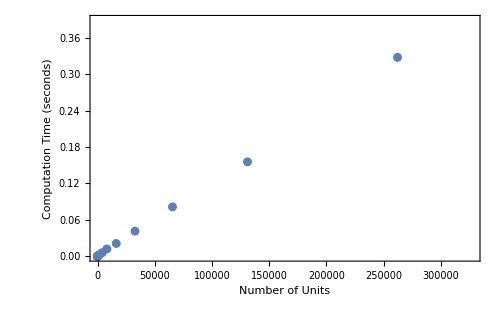

```mathematica
ListPlot[timingData[[All,1;;2]], Frame->True, FrameLabel-> {"Number of Units","Computation Time (seconds)"},ImageSize->500, BaseStyle->18]
```

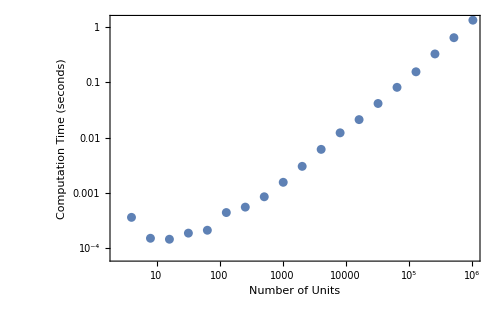

```mathematica
ListLogLogPlot[timingData[[All,1;;2]], Frame->True, FrameLabel-> {"Number of Units","Computation Time (seconds)"},ImageSize->500, BaseStyle->18]
```

The total time we need to do 1 experiment for up to 2^20=1048576 units is about 2 seconds:

```mathematica
Total[timingData[[All,2]]]
```

2.6371

If we do all the angles in parallel for 2^2 to 2^20 units (i.e., ParallelTable) it takes about 0.5 minute (4 CPUs)

```mathematica
AbsoluteTiming[result=
ParallelTable[
Table[α->{2^units,randomCorrelatedDisplacement[2^units, α]},{units,2,20}],
{α,Pi/6,4Pi,Pi/6}
];
]
```

{26.7547,Null}

Supposing we had enough patience to wait  1 hour, we could only do 100 repeated experiments.

This is likely insufficient for good statistics.

Another approach would be to do a single experiment for a large number of units, and then use the data from smaller subsequences of steps from that data.

This would produce correlations in the data, so it is not ideal.

So, if our patience limit is 10 minutes, we would do  500 Monte Carlo repetitions for up to 2^16 molecular units

```mathematica
AbsoluteTiming[
With[{monteCarloExperiments =500, nExponent=16},
correlatedRandomWalkData =
Join[<|"Monte Carlo Experiments"->monteCarloExperiments|>, Association[
ParallelTable[
(*Print[{α,DateString[]}];*)
<|α->
With[{walkExperiments =
Table[randomCorrelatedWalk[2^nExponent, α],monteCarloExperiments]
},
Association@Table[
2^n-><|
"Mean"->Mean[Norm/@walkExperiments[[All,2^n]]],"Standard Deviation"-> StandardDeviation[Norm/@walkExperiments[[All,2^n]]],
"Mean Direction"->Mean[walkExperiments[[All,2^n]]-walkExperiments[[All,2^n -1]] ]|>,
{n,1,nExponent}]
]|>,
{α,Pi/6,4Pi,Pi/6}
]
]
];
]
]
```

{564.603,Null}

Or, if we don’ t want to wait, we can grab that data as follows:

```mathematica
(*cloudData =CloudSave[correlatedRandomWalkData,"correlatedRandomWalkData_n=500_exp=16",Permissions->"Public"]*)
```

```mathematica
correlatedRandomWalkData=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/gvarnavi/correlatedRandomWalkData_n=500_exp=16"](https://www.wolframcloud.com/obj/gvarnavi/correlatedRandomWalkData_n=500_exp=16)]];
```

Let’s inspect the Keys

```mathematica
Keys[correlatedRandomWalkData]
```

{Monte Carlo Experiments,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π,(13 π)/6,(7 π)/3,(5 π)/2,(8 π)/3,(17 π)/6,3 π,(19 π)/6,(10 π)/3,(7 π)/2,(11 π)/3,(23 π)/6,4 π}

```mathematica
correlatedRandomWalkData["Monte Carlo Experiments"]
```

500

```mathematica
correlatedRandomWalkData[Pi/6]
```

<|2→<|Mean→1.99895,Standard Deviation→0.00106637,Mean Direction→{0.995672,0.000118552,-0.000244191}|>,4→<|Mean→3.99471,Standard Deviation→0.00431241,Mean Direction→{0.991261,0.000139108,0.000265553}|>,8→<|Mean→7.97811,Standard Deviation→0.0185919,Mean Direction→{0.983608,-0.000622536,-0.00101542}|>,16→<|Mean→15.9113,Standard Deviation→0.0780901,Mean Direction→{0.966309,0.000260751,0.00423202}|>,32→<|Mean→31.6453,Standard Deviation→0.285248,Mean Direction→{0.938507,0.00493496,-0.0110607}|>,64→<|Mean→62.5791,Standard Deviation→1.21788,Mean Direction→{0.874448,0.0105286,-0.0226073}|>,128→<|Mean→121.954,Standard Deviation→5.07272,Mean Direction→{0.750558,-0.0131566,0.00662919}|>,256→<|Mean→233.705,Standard Deviation→16.6357,Mean Direction→{0.557422,-0.00144553,-0.0307528}|>,512→<|Mean→425.602,Standard Deviation→60.1189,Mean Direction→{0.306701,-0.00699953,0.014109}|>,1024→<|Mean→721.497,Standard Deviation→169.401,Mean Direction→{0.0574858,-0.0107043,-0.0100769}|>,2048→<|Mean→1132.1,Standard Deviation→351.145,Mean Direction→{-0.0393968,-0.0217184,0.0079844}|>,4096→<|Mean→1732.5,Standard Deviation→614.29,Mean Direction→{-0.010396,-0.0182795,-0.0311207}|>,8192→<|Mean→2476.73,Standard Deviation→956.469,Mean Direction→{-0.00765427,-0.000485361,-0.0214391}|>,16384→<|Mean→3533.39,Standard Deviation→1482.58,Mean Direction→{0.0385961,0.0285482,-0.00829169}|>,32768→<|Mean→5111.05,Standard Deviation→2149.14,Mean Direction→{0.013593,-0.00810651,-0.0207715}|>,65536→<|Mean→7244.93,Standard Deviation→3020.45,Mean Direction→{0.0478249,-0.00216913,-0.00936071}|>|>

```mathematica
correlatedRandomWalkData[Pi/6][[All,"Mean"]]
```

<|2→1.99895,4→3.99471,8→7.97811,16→15.9113,32→31.6453,64→62.5791,128→121.954,256→233.705,512→425.602,1024→721.497,2048→1132.1,4096→1732.5,8192→2476.73,16384→3533.39,32768→5111.05,65536→7244.93|>

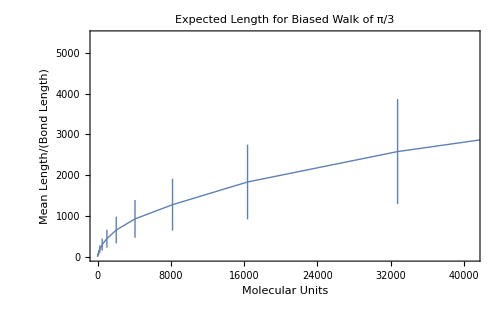

```mathematica
With[{means = correlatedRandomWalkData[Pi/3][[All,"Mean"]],
deviations = correlatedRandomWalkData[Pi/3][[All,"Mean"]]},
ListLinePlot[
MapThread[Around[#1,#2]&,{means,deviations/2}],Frame->True,FrameLabel->{"Molecular Units","Mean Length/(Bond Length)"},ImageSize->500,BaseStyle->{FontSize->18,Thick},PlotLabel->"Expected Length for Biased Walk of π/3"]
]
```

Let’s visualize all of them together

```mathematica
correlatedRandomWalkPlotData[randomWalkData_,α_]:=
MapThread[Around[#1,#2/2]&,{randomWalkData[α][[All,"Mean"]],randomWalkData[α][[All,"Standard Deviation"]]}
]
```

```mathematica
correlatedRandomWalkPlotData[correlatedRandomWalkData,Pi/6]
```

<|2→1.99890.0005,4→3.99470.0022,8→7.9780.009,16→15.910.04,32→31.650.14,64→62.60.6,128→122.02.5,256→234.8.,512→426.30.,1024→721.85.,2048→1132.176.,4096→1733.307.,8192→2477.478.,16384→3533.741.,32768→5.11.110^3,65536→7.21.510^3|>

```mathematica
DynamicModule[{allMeans=(correlatedRandomWalkData[#1]⟦All,"Mean"⟧&)/@Range[π/6,4 π,π/6],meansAndSDs=Association[(#1->correlatedRandomWalkPlotData[correlatedRandomWalkData,#1]&)/@Range[π/6,4 π,π/6]],background},background=ListLinePlot[allMeans,PlotRange->All,Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"Molecular Units","Mean Length"},AspectRatio->2/8,ImageSize->500,PlotLabel->"Expected Length for Biased Walk",ImageMargins->0];Manipulate[ListLinePlot[meansAndSDs[α],PlotRange->All,PlotStyle->Black,AspectRatio->1/2,Frame->True,FrameLabel->{"Molecular Units","Mean Length"},BaseStyle->{FontSize->18},ImageSize->500,PlotLabel->"Expected Length for Biased Walk"],{{α,π/2,Style["Solid Angle Bias",14]},Range[π/6,4 π,π/6]},Dynamic[Show[background,ListLinePlot[meansAndSDs[α],FrameLabel->{"Molecular Units","Mean Length/(Bond Length)"},PlotStyle->{Black,Thickness[0.005]}]]],Paneled->False]
]
```

If the solid angle α = 0, then we would expect the length to grow linearly with the number of units because the polymer would be straight.

How does the fit we found above   change with α?

Let’s rearrange the data into a list:

```mathematica
With[{keys =Keys[correlatedRandomWalkData[Pi/6]], values =Values [correlatedRandomWalkData[Pi/6][[All,"Mean"]]]},
Transpose[{keys, values}]
]
```

{{2,1.99895},{4,3.99471},{8,7.97811},{16,15.9113},{32,31.6453},{64,62.5791},{128,121.954},{256,233.705},{512,425.602},{1024,721.497},{2048,1132.1},{4096,1732.5},{8192,2476.73},{16384,3533.39},{32768,5111.05},{65536,7244.93}}

Even for highly correlated bond angles, the expected length scales as :

```mathematica
With[{
keys =Keys[correlatedRandomWalkData[Pi/6]],
values =Values [correlatedRandomWalkData[Pi/6][[All,"Mean"]]],
model = a + b n^p},
FindFit[Transpose[{keys, values}],model, {a,b,p},n]
]
```

{a→-112.23,b→25.1297,p→0.512593}

However, if we look at  limited range of data, we can see that the power law exponent shifts from 1 to 1/2.

That is, the polymer morphology has a "correlation length"

```mathematica
DynamicModule[{keys,values,fit,data,fitParameters,a,b,p,n,model},model=a+b n^p;Manipulate[keys=Keys[correlatedRandomWalkData[α]];values=Values[correlatedRandomWalkData[α]⟦All,"Mean"⟧];data=Transpose[{keys,values}]⟦1;;last⟧;fitParameters=FindFit[data,model,{a,b,p},n];fit=model/.fitParameters;Show[ListPlot[data,PlotRange->{{0,2^last},All},Frame->True,AxesOrigin->{0,0},ImageSize->500,BaseStyle->{FontSize->16},FrameLabel->{"Number of Molecular Units","Expected Length/(Bond Length)"}],Plot[fit,{n,1,2^last}]],{{last,3,Style["Number of Units",16]},(#1->2^#1&)/@Range[16]},Dynamic[Style["Power Law Fit: "<>ToString[p/.fitParameters],16]],{{α,π/6,Style["Correlation Angle",16]},Range[π/6,4 π,π/6],ControlType->SetterBar},Paneled->False]]
```

In our association, we also have data for the last bond direction

```mathematica
correlatedRandomWalkData[Pi/6][[All,"Mean Direction"]]
```

<|2→{0.995672,0.000118552,-0.000244191},4→{0.991261,0.000139108,0.000265553},8→{0.983608,-0.000622536,-0.00101542},16→{0.966309,0.000260751,0.00423202},32→{0.938507,0.00493496,-0.0110607},64→{0.874448,0.0105286,-0.0226073},128→{0.750558,-0.0131566,0.00662919},256→{0.557422,-0.00144553,-0.0307528},512→{0.306701,-0.00699953,0.014109},1024→{0.0574858,-0.0107043,-0.0100769},2048→{-0.0393968,-0.0217184,0.0079844},4096→{-0.010396,-0.0182795,-0.0311207},8192→{-0.00765427,-0.000485361,-0.0214391},16384→{0.0385961,0.0285482,-0.00829169},32768→{0.013593,-0.00810651,-0.0207715},65536→{0.0478249,-0.00216913,-0.00936071}|>

Since the first step is always {1,0,0}, the first component of the mean direction is a measure of the correlation to the first bond.

For α = π/6, the correlation disappears after about 1000 units.

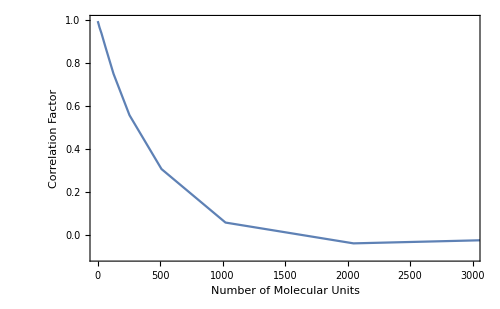

```mathematica
ListLinePlot[First/@correlatedRandomWalkData[Pi/6][[All,"Mean Direction"]],
Frame->True,PlotRange->{{0,3000},{-0.1,1}},ImageSize->500,BaseStyle->{FontSize->14},FrameLabel->{"Number of Molecular Units","Correlation Factor"}]
```

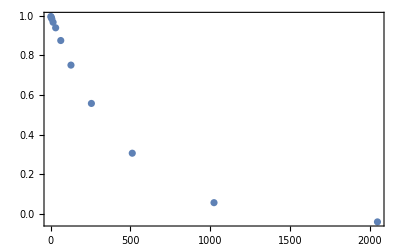

```mathematica
limitedData =With[{keys =Keys[correlatedRandomWalkData[Pi/6]], values =First/@Values [correlatedRandomWalkData[Pi/6][[All,"Mean Direction"]]]},
Transpose[{keys, values}][[1;;11]]
];
limitedDataPlot =ListPlot[limitedData,Frame->True]
```

We can use this limited data to fit a correlation length

I.e. The length at which correlations decay exponentially

```mathematica
correlationFit =With[{correlationModel = Exp[-n/η]},FindFit[limitedData,correlationModel,η,n]]
```

{η→427.287}

The characteristic correlation length is about 420 molecular units

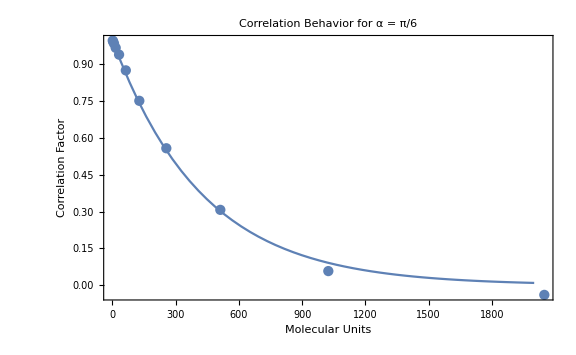

```mathematica
With[{correlationModel = Exp[-n/η]},
Show[ListPlot[limitedData],Plot[correlationModel/.correlationFit,{n,0,2000}],ImageSize->Large,Frame->True, FrameLabel-> {"Molecular Units","Correlation Factor"},
PlotLabel->"Correlation Behavior for α = π/6", BaseStyle->{FontSize->16}]]
```

For α = 2π (i.e., the polymer never “bends backwards” )

The  correlation has effectively vanished after 3 about steps.

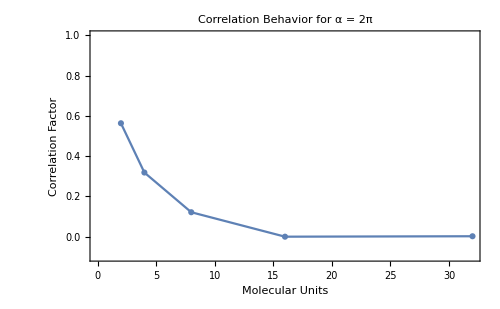

```mathematica
ListLinePlot[With[{keys=Keys[correlatedRandomWalkData[2 π]],values=First/@Values[correlatedRandomWalkData[2 π]⟦All,"Mean Direction"⟧]},Transpose[{keys,values}]⟦1;;5⟧],ImageSize->500,Frame->True,FrameLabel->{"Molecular Units","Correlation Factor"},PlotMarkers->Automatic,PlotLabel->"Correlation Behavior for α = 2π",BaseStyle->{FontSize->16},PlotRange->{{0,2^5},{-0.1,1}}]
```

If we look at the behavior of a single polymer with α=π/3:

```mathematica
path= randomCorrelatedWalk[2^12, Pi/3];
Graphics3D[Tube[path]]//Rasterize
```

-Graphics-

We can see that the correlation is a random walk on a sphere where the step size is the solid angle α

```mathematica
Graphics3D[Tube[Differences@path]]//Rasterize
```

-Graphics-

## Polymer Microstructures

Let’s go back to 2D and try generating non-intersecting polymer chains with correlations

We’ll then try assembling a number of them together

This will set us up well to study step-wise polymerization next week

First - let’s write a simple function to return a polymer with N molecular units and some correlation

It will be convenient to define a “correlation” variable

Which has a value of 1 when the polymer is “maximally” correlated (i.e. the next bond angle is chosen from a range {0,0})

and a value of 0 when the polymer is uncorrelated (i.e. the next bond angle is chosen from the full range of angles {-π,π})

```mathematica
Simplify[Rescale[correlation,{0,1},{-π,0}]]
```

(-1+correlation) π

```mathematica
angularRange[correlation_]:={-1,1}(1-correlation)π
```

```mathematica
angularRange[0]
```

{-π,π}

```mathematica
angularRange[1]
```

{0,0}

Let’s write a simple visualization function to help us debug

```mathematica
visualizeChain[sortedParticles_,bondDistance_:1]:=Block[{start,end,rest,n=Length[sortedParticles],r=bondDistance/2},
{{start},rest,{end}}=TakeList[sortedParticles,{1,n-2,1}];
Graphics[{
{RGBColor[0,1/3,0],Disk[#,r]&/@rest},
{Orange,Disk[#,r]&/@{start,end}},
{Black,BSplineCurve[sortedParticles]}
}
]
]
```

And write a simple function like we had above

```mathematica
correlatedPolymerChain2D[numberUnits_,correlation_]:=AnglePath[RandomReal[angularRange[correlation],numberUnits-1]]
```

```mathematica
visualizeChain[correlatedPolymerChain2D[12,0.2]]
```

-Graphics-

It’s clear this naive approach very quickly leads to self-intersections

Let’s instead write a function to be appending one particle at a time

while checking for collisions

Our first step is to write a collision-detection function

The simplest idea is to compute the distance b/w all the particles

And check no-distances are less than

Distance between two particles

```mathematica
EuclideanDistance[{x1,y1},{x2,y2}]
```

√(Abs[x1-x2]^2+Abs[y1-y2]^2)

Distances between all particles

```mathematica
MatrixForm[Outer[EuclideanDistance,{{x1,y1},{x2,y2},{x3,y3}},{{x1,y1},{x2,y2},{x3,y3}},1]]
```

(0 | √(Abs[x1-x2]^2+Abs[y1-y2]^2) | √(Abs[x1-x3]^2+Abs[y1-y3]^2)
√(Abs[-x1+x2]^2+Abs[-y1+y2]^2) | 0 | √(Abs[x2-x3]^2+Abs[y2-y3]^2)
√(Abs[-x1+x3]^2+Abs[-y1+y3]^2) | √(Abs[-x2+x3]^2+Abs[-y2+y3]^2) | 0)

This is rather wasteful since the “Distance Matrix” is symmetric, so we only need to compute half-of it

In-fact less than half, N(N-1)/2 entries, since the diagonal is by definition 0

If you’re curious about all the ways to calculate pairwise distances in the WL - there’s a nice SE post about it here:

https://mathematica.stackexchange.com/questions/21861/fastest-way-to-calculate-matrix-of-pairwise-distances

The built-in `DistanceMatrix` function is actually reasonably fast (on numeric points)

```mathematica
MatrixForm[DistanceMatrix[{{x1,y1},{x2,y2},{x3,y3}},DistanceFunction->EuclideanDistance]]
```

(0 | √Abs[Abs[x1-x2]^2+Abs[y1-y2]^2] | √Abs[Abs[x1-x3]^2+Abs[y1-y3]^2]
√Abs[Abs[x1-x2]^2+Abs[y1-y2]^2] | 0 | √Abs[Abs[x2-x3]^2+Abs[y2-y3]^2]
√Abs[Abs[x1-x3]^2+Abs[y1-y3]^2] | √Abs[Abs[x2-x3]^2+Abs[y2-y3]^2] | 0)

One quick common trick on Distance matrices is that often times if we want to compare distances we can just use SquaredEuclideanDistance and compare against bond_length^2

This saves us having to compute the outermost square root in all the entries above!

However, this still does more work than we need it to

Remember we’ll actually be building this polymer chain incrementally

I.e. we only need to check if the point we’re trying to add collides with any of the existing points

Since the previous points have already been checked

We can do this efficiently using `Nearest`

This uses a KDtree implementation - ask me about it if there’s time!

Essentially we’ll build a fast look-up table of the existing particles - and then find the nearest particle to our candidate

If that distance is less than the bond angle - there’s a collision

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]["Distance"]<bondLength
```

```mathematica
chainSoFar=correlatedPolymerChain2D[6,0.4];
visualizeChain[chainSoFar]
```

-Graphics-

Let’s debug this visually

```mathematica
Block[{nf=Nearest[chainSoFar->All],lastAngle,newAngle,candidate,angleRange=angularRange[0.4]},
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]);
newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];
Echo[collisionQ[nf][candidate]];
visualizeChain[Append[chainSoFar,candidate]]
]
```

False

-Graphics-

Seems to work!

Let’s write this into a function

```mathematica
addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->All],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]/;Length[chainSoFar]>1
```

```mathematica
Dynamic[visualizeChain[chainSoFar]]
```

```mathematica
Do[
chainSoFar=addCorrelatedParticleToChain[0.4][chainSoFar];
Pause[0.5],{10}]
```

Great, works as expected!

So finally, let’s wrap this in a function to compute N-molecular unit polymers

This is a job for NestWhile!

```mathematica
?NestWhile
```

```mathematica
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,maxAttempts_:100]:=NestWhile[addCorrelatedParticleToChain[correlation],correlatedPolymerChain2D[2,correlation],Length[#]<numberUnits&,1,maxAttempts]
```

```mathematica
Multicolumn[visualizeChain[collisionFreeCorrelatedPolymerChain2D[#,0.4]]&/@RandomInteger[{6,18},12],6,Frame->All]
```

-Graphics-